MatrixForm

Null

Null

Null

«3 more identical outputs»

m w^2 x[t]+2 m w y'[t]

Null

Null

(98 (0.4 t Cos[0.4 t]-Sin[0.4 t])
-98 (Cos[0.4 t]+0.4 t Sin[0.4 t]))

Null

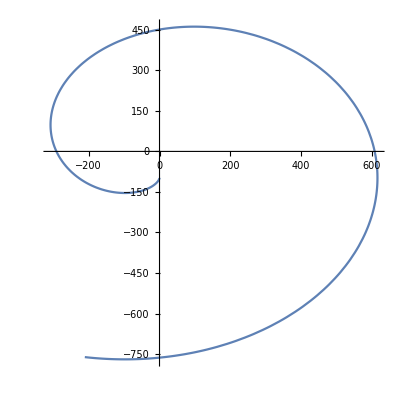

Null

Null

Null

```mathematica
(*Construct the r vector and velocity vector functions.*)
$Post = MatrixForm
rvec[t_] = {x[t],y[t]};
Vvec[t_] = D[rvec[t],t];
rvec3D = {x[t],y[t],0};
(*spin vector for our spaceship!! (pointing out of page)*)
wvec = {0,0,w};
(*Our ficticious forces*)
Fcent = - m (Cross[wvec,Cross[wvec,rvec3D]]);
Fcor = -2 m Cross[wvec,D[rvec3D,t]];
Dot[(Fcent + Fcor),{1,0,0}]
(*Now Begin Work on the problem*)
(*Determine start position as d*)
result =FullSimplify[ExpToTrig[DSolve[{x''[t]==Dot[(Fcent + Fcor)/m,{1,0,0}],y''[t] == Dot[(Fcent + Fcor)/m,{0,1,0}],x'[0] == 0, x[0]== 0, y'[0] == 0, y[0] == -d},{x[t],y[t]},t]]];
params = {R -> 100, d -> 98, w -> .4};
(*Parametric Plot*)
{(x[t]/.result)/. params,(y[t]/.result)/. params}
pt[t_] = {98 (0.4 t Cos[0.4 t]-Sin[0.4 t]),-98 (Cos[0.4 t]+0.4 t Sin[0.4 t])};
curve = ParametricPlot[pt[t],{t,0,20}, AspectRatio->1] 
circle = With[{r = 200} , {
{Opacity[.1],Blue,Disk[{0,0},r]},
{Opacity[.15],Blue,
Table[Line[{{x,-Sqrt[r^2-x^2]},{x,+Sqrt[r^2-x^2]}}],{x,-r,r,r/10}],
Table[Line[{{-Sqrt[r^2-y^2],y},{+Sqrt[r^2-y^2],y}}],{y,-r,r,r/10}]
}}];
graphicsobjects = {circle,curve[[1]]};
Graphics[ graphicsobjects];
Animate[Graphics[{graphicsobjects,{Black,PointSize[.03],Point[{pt[t]}]}}],{t,0,20}]
```

```mathematica
Dimensions[{{98 (0.4 t Cos[0.4 t]-Sin[0.4 t])},{-98 (Cos[0.4 t]+0.4 t Sin[0.4 t])}}]
```

(2
1)

```mathematica
Times@@{2,1}
```

2